### Mapping Gaussian Points

Gaussian integers are prime in only 3 possible cases:
	Case 1:Norm(π) = p and p ≡1 mod 4 
	OR
	Case 2:π = p, p is prime and p ≡3 mod 4
	Case 3: Norm(π) = 2
Any Gaussian integer has 4 associates.  For each π where π = p and p ≡ 1 mod 4, there are 8 total prime Gaussian integers.  For each π = p, p is prime and p ≡ 3 mod 4, there are 4 total prime Gaussian integers
Using the list of primes available in Mathematica, we can easily zero on the Gaussian primes
The trick will be translating the results to all possible corresponding points

### Generating Points for case 1

```mathematica
(*Generate the 8 points with norm = p, it's assumed that p is prime and congruent to 1 mod 4
 PowersRepresentations returns a list of tuples that satisfy the equation.  From a theorem by
 Fermat, the represenation of a prime, p, ≡ 1 mod 4 as a sum of squares is unique, so don't
 need to worry about a list of multiple results *)
mod1SquarePoints[p_, sideLength_] :=
Module[{squares = Flatten[PowersRepresentations[p,2,2]]},
x = squares[[1]];
y = squares[[2]];
If[x <= sideLength && y <= sideLength,Return[{{x,y},{x,-y},{-x,y},{-x,-y}, {y,x},{y,-x},{-y,x},{-y,-x}}], Return[{{1,1}}]]]

mod1SquarePoints[1^2 + 14^2, 20]
```

{{1,14},{1,-14},{-1,14},{-1,-14},{14,1},{14,-1},{-14,1},{-14,-1}}

### Generating Points for case 2

```mathematica
mod3SquarePoints[p_] := Return[{{p,0},{-p,0},{0,p},{0,-p}}]

mod3Points[7]
```

{7,0}

### Put the cases together to generate a function for producing Gaussian points Let’s assume you want to display the primes in a given square of size s x s, where the side s has half of it’s length in one quadrant and other half in the adjacent quadrant A prime, p, will correspond to a point p^1/2 from the origin (assuming congruent to 1 mod 4). So if you want a graph that gives you a square of size s x s, the farthest possible point congruent to 1 mod 4 will have norm = (s/2)^2 + (s/2)^2 or 2 * (s/2)^2 For those points corresponding to a prime, p, congruent to 3 mod 4, only find the corresponding points if the prime <= s/2 The max distance you want to explore will determine the primes you want to explore For those primes under case 1, explore primes <= distance^2 since we are using the fact that N(π) = prime, x is the distance, so x = prime^1/2 For those primes under case 2, explore primes <= distance/2

```mathematica
generatePointsInSquare[p_, sideLength_] := If[Mod[p, 4]== 1 && p ≤ 2(sideLength/2)^2, mod1SquarePoints[p, sideLength/2], If[p ≤ sideLength/2, mod3SquarePoints[p], {{0,0}}]]

Mod[1^2 + 14^2, 4]
generatePointsInSquare[1^2 + 14^2,20]
```

1

{{1,1}}

### Iterate through the prime numbers and generate the Gaussian primes How many primes should you use? Assuming for now that we’re generating all possible points in a square, given a side length of s, the farthest possible point from the origin will correspond to a prime congruent to 1 mod 4, and will have norm of 2 * (s/2)^2. We can use the Mathematica PrimePi, function to tell us how many primes are less than or equal to a number. In our case, that number is 2 * (s/2)^2.

```mathematica
squareSize = 20;
numberOfPrimes = PrimePi[2*(squareSize/2)^2]
```

46

```mathematica
numPrimes[sideLength_] := PrimePi[2 * (sideLength/2)^2]
numPrimes[30]
root2Primes = {{1,1},{1,-1},{-1,1},{-1,-1}};
gaussianPoints =DeleteCases[Union[Flatten[Map[generatePointsInSquare[#,squareSize]&, Table[Prime[n],{n,2,numPrimes[squareSize]}]],1],root2Primes], {0,0}]
```

87

{{-10,-9},{-10,-7},{-10,-3},{-10,-1},{-10,1},{-10,3},{-10,7},{-10,9},{-9,-10},{-9,-4},{-9,4},{-9,10},{-8,-7},{-8,-5},{-8,-3},{-8,3},{-8,5},{-8,7},{-7,-10},{-7,-8},{-7,-2},{-7,0},{-7,2},{-7,8},{-7,10},{-6,-5},{-6,-1},{-6,1},{-6,5},{-5,-8},{-5,-6},{-5,-4},{-5,-2},{-5,2},{-5,4},{-5,6},{-5,8},{-4,-9},{-4,-5},{-4,-1},{-4,1},{-4,5},{-4,9},{-3,-10},{-3,-8},{-3,-2},{-3,0},{-3,2},{-3,8},{-3,10},{-2,-7},{-2,-5},{-2,-3},{-2,-1},{-2,1},{-2,3},{-2,5},{-2,7},{-1,-10},{-1,-6},{-1,-4},{-1,-2},{-1,-1},{-1,1},{-1,2},{-1,4},{-1,6},{-1,10},{0,-7},{0,-3},{0,3},{0,7},{1,-10},{1,-6},{1,-4},{1,-2},{1,-1},{1,1},{1,2},{1,4},{1,6},{1,10},{2,-7},{2,-5},{2,-3},{2,-1},{2,1},{2,3},{2,5},{2,7},{3,-10},{3,-8},{3,-2},{3,0},{3,2},{3,8},{3,10},{4,-9},{4,-5},{4,-1},{4,1},{4,5},{4,9},{5,-8},{5,-6},{5,-4},{5,-2},{5,2},{5,4},{5,6},{5,8},{6,-5},{6,-1},{6,1},{6,5},{7,-10},{7,-8},{7,-2},{7,0},{7,2},{7,8},{7,10},{8,-7},{8,-5},{8,-3},{8,3},{8,5},{8,7},{9,-10},{9,-4},{9,4},{9,10},{10,-9},{10,-7},{10,-3},{10,-1},{10,1},{10,3},{10,7},{10,9}}

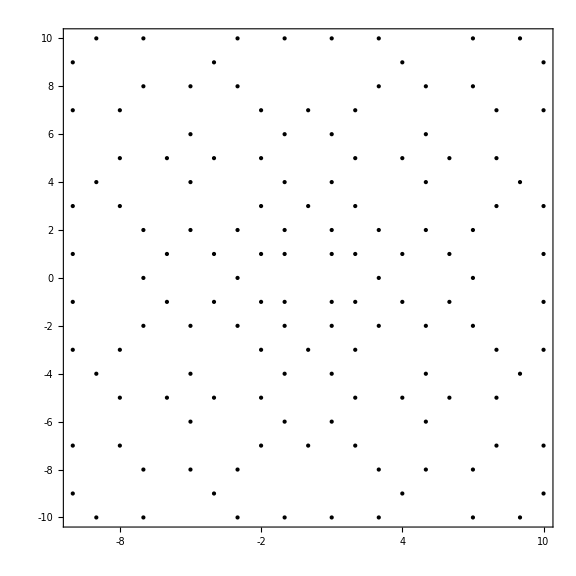

```mathematica
Graphics[Point[gaussianPoints], Frame->True, FrameTicks->{{Range[-10,10,1],None},{Range[-20,20,1],None}}, ImageSize->Large]
```

```mathematica
gaussianPrimePoints[squareSize_] := Union[Flatten[Map[generatePointsInSquare[#,squareSize]&, Table[Prime[n],{n,2,numPrimes[squareSize]}]],1],root2Primes]
gaussianPrimePoints[10]
```

{{-5,-4},{-5,-2},{-5,2},{-5,4},{-4,-5},{-4,-1},{-4,1},{-4,5},{-3,-2},{-3,0},{-3,2},{-2,-5},{-2,-3},{-2,-1},{-2,1},{-2,3},{-2,5},{-1,-4},{-1,-2},{-1,-1},{-1,1},{-1,2},{-1,4},{0,-3},{0,0},{0,3},{1,-4},{1,-2},{1,-1},{1,1},{1,2},{1,4},{2,-5},{2,-3},{2,-1},{2,1},{2,3},{2,5},{3,-2},{3,0},{3,2},{4,-5},{4,-1},{4,1},{4,5},{5,-4},{5,-2},{5,2},{5,4}}

```mathematica
Manipulate[Graphics[Point[gaussianPrimePoints[z]], Frame->True, FrameTicks->{{Range[-100,100,2],None},{Range[-100,100,2],None}}, ImageSize->Large], {z, 4, 100,2}]
```